# Exercise 1.1

## Band structure of SSH model with open boundary conditions (OBC).

The following cells can be neglected: they contain simple coding to break the ice with the problem.

```mathematica
ClearAll;
mu=0.5; (*v/w ratio*)
n=15; (*number of unit cells*)
H=SparseArray[{{i_,j_}/;j==i+1&&Mod[j,2]==1->1.,
{i_,j_}/;j==i-1&&Mod[j,2]==0->1.,
{i_,j_}/;j==i+1&&Mod[j,2]==0->mu,
{i_,j_}/;j==i-1&&Mod[j,2]==1->mu},
{2n,2n},0.];(*2n x 2n hamiltonian matrix in real space with OBC*)
```

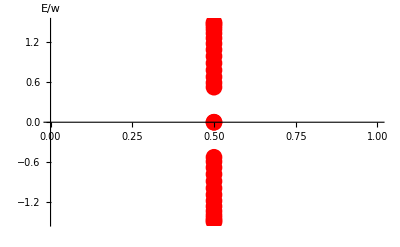

{0.0000228882}

```mathematica
(*Plot energy bands*)
(*Observation: mu>1 -> no states in the gap; mu<1 -> two states in the middle *)
energy=Eigenvalues[H];
ListPlot[Table[{mu,energy[[i]]},{i,1,2n}],
PlotStyle->{Red,PointSize[.03]},Ticks->{None,Automatic},AxesStyle->Directive[Black, 12],AxesLabel->{None,"E/w"}]
Eigenvalues[H,-1]
```

The following cell evaluates the energy bands of SSH model with open boundary conditions as a function of μ=v/w. The number of unit cells is fixed in the plot and can be chosen by the user. It turns out that  for μ<1 there exists a couple of energy states inside the bands, called edge states. The edge states disappear as μ>1.

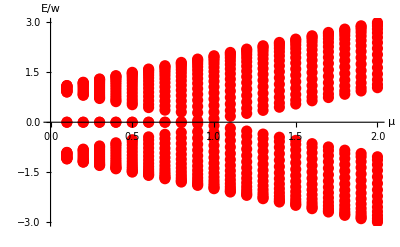

```mathematica
ClearAll;
n=15;
bands={};
For[mu=0.1,mu≤ 2.0,mu+=0.1,
H=SparseArray[{{i_,j_}/;j==i+1&&Mod[j,2]==1->1.,
{i_,j_}/;j==i-1&&Mod[j,2]==0->1.,
{i_,j_}/;j==i+1&&Mod[j,2]==0->mu,
{i_,j_}/;j==i-1&&Mod[j,2]==1->mu},
{2n,2n},0.];
energy=Eigenvalues[H];
For[i=1,i≤2n,i++,
AppendTo[bands,{mu,energy[[i]]}];
]
]
ListPlot[bands,PlotStyle->{PointSize[.02],Red},AxesLabel->{"μ","E/w"},AxesStyle->Directive[Black, 12]]
```

The following cell evaluates the gap between the two edge states as a function of the number of unit cells n. In this case the parameter μ is fixed by the user. Pay attention to chose μ<1.

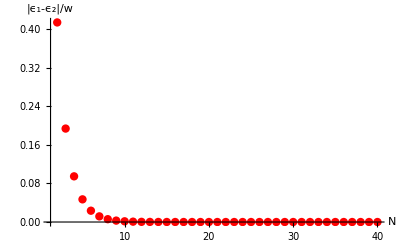

```mathematica
(*Show energy difference between edge states as a function of n *)
ClearAll;
mu=0.5;
list={};
For[k=2,k≤ 40,k+=1,
H=SparseArray[{{i_,j_}/;j==i+1&&Mod[j,2]==1->1.,
{i_,j_}/;j==i-1&&Mod[j,2]==0->1.,
{i_,j_}/;j==i+1&&Mod[j,2]==0->mu,
{i_,j_}/;j==i-1&&Mod[j,2]==1->mu},
{2k,2k},0.];
e1=Eigenvalues[H,-1];
AppendTo[list,{k,2*Abs[e1[[1]]]}];
]
ListPlot[list,PlotStyle->{Red,PointSize[.015]},AxesLabel->{"N","|ϵ_1-ϵ_2|/w"},AxesStyle->Directive[Black, 12],PlotRange->All]
```

The following cell evaluates the two edge eigenstates at fixed μ and N. It turns out that the even components are zero.

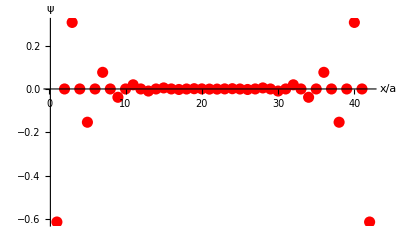

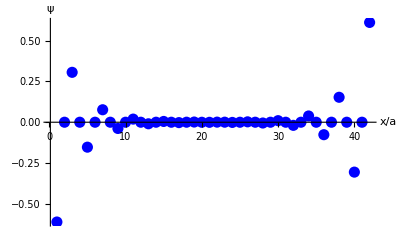

```mathematica
ClearAll;
mu=0.5;
n=21;
H=SparseArray[{{i_,j_}/;j==i+1&&Mod[j,2]==1->1.,
{i_,j_}/;j==i-1&&Mod[j,2]==0->1.,
{i_,j_}/;j==i+1&&Mod[j,2]==0->mu,
{i_,j_}/;j==i-1&&Mod[j,2]==1->mu},
{2n,2n},0.];
{psi1,psi2}=Eigenvectors[H,-2];
ListPlot[psi1,PlotRange->All,PlotStyle->{Red,PointSize[.02]},AxesLabel->{"x/a","ψ"},AxesStyle->Directive[Black, 12]]
ListPlot[psi2,PlotRange->All,PlotStyle->{Blue,PointSize[.02]},AxesLabel->{"x/a","ψ"},AxesStyle->Directive[Black, 12]]
```

## Band structure of SSH model with periodic boundary conditions (PBC).

Let’s evaluate the band structure as a function of μ in the system with PBC. The important difference is that in this case there are no edge states.

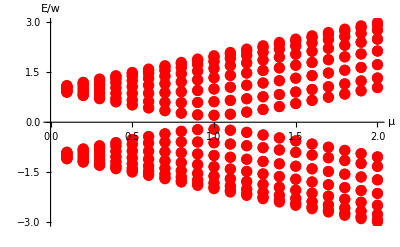

```mathematica
ClearAll;
n=15;
bands={};
For[mu=0.1,mu≤ 2.0,mu+=0.1,
H=SparseArray[{{i_,j_}/;j==i+1&&Mod[j,2]==1->1.,
{i_,j_}/;j==i-1&&Mod[j,2]==0->1.,
{i_,j_}/;j==i+1&&Mod[j,2]==0->mu,
{i_,j_}/;j==i-1&&Mod[j,2]==1->mu,
{i_,j_}/;Abs[j-i]==2n-1-> 1},
{2n,2n},0.];
energy=Eigenvalues[H];
For[i=1,i≤2n,i++,
AppendTo[bands,{mu,energy[[i]]}];
]
]
ListPlot[bands,PlotStyle->{PointSize[.02],Red},AxesLabel->{"μ","E/w"},AxesStyle->Directive[Black, 12]]
```

In order to check the correct behaviour of our numerical simulation, we can compare it to the exact results. In particular we know that the bands are

|v-w|<E_+<|v+w| → |μ-1|<E_+/w<|μ+1|

And a similar relation holds for the lower band.

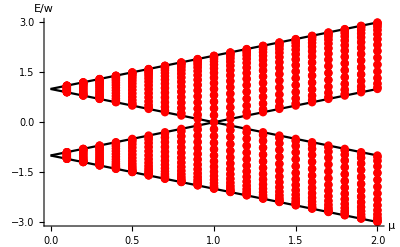

```mathematica
ClearAll;
f[μ_]:=Abs[μ-1];
g[μ_]:=Abs[μ+1];
pl=Plot[{f[x],g[x],-f[x],-g[x]},{x,0,2},PlotStyle->{Black,Black,Black,Black},PlotRange->All,AxesLabel->{"μ","E/w"},AxesStyle->Directive[Black, 12]];
n=30;
bands={};
For[mu=0.1,mu≤ 2.0,mu+=0.1,
H=SparseArray[{{i_,j_}/;j==i+1&&Mod[j,2]==1->1.,
{i_,j_}/;j==i-1&&Mod[j,2]==0->1.,
{i_,j_}/;j==i+1&&Mod[j,2]==0->mu,
{i_,j_}/;j==i-1&&Mod[j,2]==1->mu,
{i_,j_}/;Abs[j-i]==2n-1-> 1},
{2n,2n},0.];
energy=Eigenvalues[H];
For[i=1,i≤2n,i++,
AppendTo[bands,{mu,energy[[i]]}];
]
]
lp=ListPlot[bands,PlotStyle->{PointSize[.015],Red},AxesLabel->{"μ","E/w"},AxesStyle->Directive[Black, 12]];
Show[pl,lp]
```